## Probabilities in NIS and NIN junction

```mathematica
Remove["Global`*"];

p=Solve[{1+b==c*u0+d*v0,a==c*v0+d*u0,c*q1*u0-d*q2*v0-k1+b*k1==-I*2*Z*(1+b),c*q1*v0-q2*d*u0-a*k2==-I*2*Z*a},{a,b,c,d}]//Simplify;

a=a/.p[[1]]//Simplify
b=b/.p[[1]]//Simplify
c=c/.p[[1]]//Simplify
d=d/.p[[1]]//Simplify
```

-(2 k1 (q1+q2) u0^2 v0)/((q1+q2) u0 v0^2 (-k1+q2-2 ⅈ Z)+u0 (-u0^2 (k1+q1+2 ⅈ Z)+v0^2 (k1-q2+2 ⅈ Z)) (k2+q2-2 ⅈ Z))

(-(u0^2-v0^2) (q2-2 ⅈ Z) (q1+2 ⅈ Z)+k1 (q2 u0^2+q1 v0^2+k2 (u0^2-v0^2)-2 ⅈ u0^2 Z+2 ⅈ v0^2 Z)-k2 (q1 u0^2+q2 v0^2+2 ⅈ (u0^2-v0^2) Z))/((u0^2-v0^2) (q2-2 ⅈ Z) (q1+2 ⅈ Z)+k1 (q2 u0^2+q1 v0^2+k2 (u0^2-v0^2)-2 ⅈ u0^2 Z+2 ⅈ v0^2 Z)+k2 (q1 u0^2+q2 v0^2+2 ⅈ (u0^2-v0^2) Z))

(2 k1 u0 (k2+q2-2 ⅈ Z))/((u0^2-v0^2) (q2-2 ⅈ Z) (q1+2 ⅈ Z)+k1 (q2 u0^2+q1 v0^2+k2 (u0^2-v0^2)-2 ⅈ u0^2 Z+2 ⅈ v0^2 Z)+k2 (q1 u0^2+q2 v0^2+2 ⅈ (u0^2-v0^2) Z))

-(2 k1 v0 (k2-q1-2 ⅈ Z))/((u0^2-v0^2) (q2-2 ⅈ Z) (q1+2 ⅈ Z)+k1 (q2 u0^2+q1 v0^2+k2 (u0^2-v0^2)-2 ⅈ u0^2 Z+2 ⅈ v0^2 Z)+k2 (q1 u0^2+q2 v0^2+2 ⅈ (u0^2-v0^2) Z))

## Scattering amplitudes in NIS with ANdreev approximation

```mathematica
a/.{q1-> 1,q2-> 1,k1-> 1,k2-> 1}//Simplify
```

(u0 v0)/(-v0^2 Z^2+u0^2 (1+Z^2))

```mathematica
b/.{q1-> 1,q2-> 1,k1-> 1,k2-> 1}//Simplify
```

-((u0^2-v0^2) Z (ⅈ+Z))/(-v0^2 Z^2+u0^2 (1+Z^2))

```mathematica
c/.{q1-> 1,q2-> 1,k1-> 1,k2-> 1}//Simplify
```

(u0-ⅈ u0 Z)/(-v0^2 Z^2+u0^2 (1+Z^2))

```mathematica
d/.{q1-> 1,q2-> 1,k1-> 1,k2-> 1}//Simplify
```

(ⅈ v0 Z)/(-v0^2 Z^2+u0^2 (1+Z^2))

## NIS to NIN in the limit u->1, v->0, Here, A becomes zero and B is non-zero.

```mathematica
A1=Abs[a]^2/.{u0->1,v0->0,q1-> k1}
```

0

```mathematica
B1=ComplexExpand[b*Conjugate[b]]/.{u0->1,v0->0,q1-> k1}//Simplify
```

Z^2/(k1^2+Z^2)

```mathematica
Tn1=ComplexExpand[c*Conjugate[c]]/.{u0->1,v0->0,q1-> k1}//Simplify
```

k1^2/(k1^2+Z^2)

```mathematica
Tn0=ComplexExpand[d*Conjugate[d]]/.{u0->1,v0->0,q1-> k1}//Simplify
```

0

## Conductance and noise in NIN junction for E dependent transmission:

## Transmission probability in NIN

```mathematica
Remove["Global`*"];

k=8.617*10^-5;
Ef=0.14;
ke=Piecewise[{{(1+Ed/Ef)^(1/2),Ed>Ef},{(1-Ed/Ef)^(1/2),Ed≤Ef}}]; 
ReeN=Z1^2/(1+Z1^2); 
TeeN=1/(1+Z1^2);
Z1=Z/ke;

FIN=(1-ReeN);
DshN=ReeN(1-ReeN);
DthN=(1-ReeN);
```

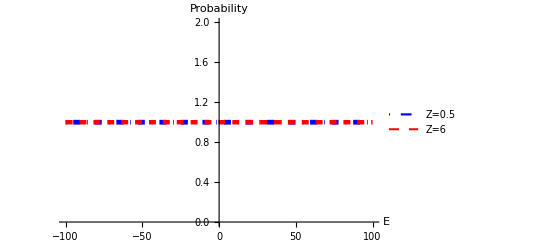

```mathematica
Plot[{(TeeN+ReeN)/.{Z-> 0.5},(TeeN+ReeN)/.{Z-> 6}},{Ed,-100,100},PlotRange->{0,2},PlotStyle->{{Blue,DotDashed,Thickness[0.0086]},{Red,Dashed,Thickness[0.008]}},PlotLegends->Placed[{Style["Z=0.5",18,Black,Bold],Style["Z=6",18,Black,Bold]},{Left,Top}],FrameTicksStyle->Directive[Black,18,Bold],AxesLabel-> {Style["E",21,Black,Bold],Style["Probability",22,Black,Bold]},LabelStyle->Directive[20,Black,Bold]]
```

```mathematica
Plot[{1-ReeN/.{Ed-> 0.002},ReeN/.{Ed-> 0.002}},{Z,.0,4.05},PlotRange->{-0.01,1.05},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["𝒯",18,Black,Bold],Style["ℛ",18,Black,Bold],Style["Z=3",18,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,19,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{1,"1.0"},{2,"2.0"},{0,"0.0"},{3,"3.0"},{4,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["Z",22,Black,Bold],Style["",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

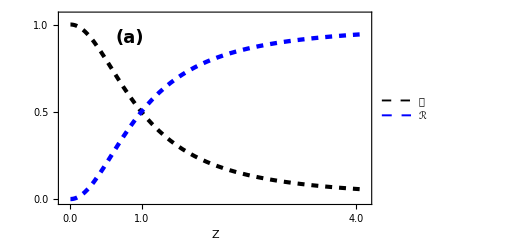

## Current in NIN at Eqbm temp vs. Z

```mathematica
Remove["Global`*"];

k=8.617*10^-5;
Ef=0.014;
ke=Piecewise[{{(1+Ed/Ef)^(1/2),Ed>Ef},{(1-Ed/Ef)^(1/2),Ed≤Ef}}]; 
ReeN=Z1^2/(1+Z1^2); 
TeeN=1/(1+Z1^2);
Z1=Z/ke;
FIN=(TeeN);
f1e=1/(1+Exp[(Ed-Ef-V1)/kT]);f2e=1/(1+Exp[(Ed-Ef)/kT]); Df0=D[(f2e),{Ed}];kT=k*T;
FI=f1e-f2e;
V1=0.00001;
listI0=ParallelTable[
thNz0= (NIntegrate[FIN*FI/.{T-> 1},{Ed,-Infinity,V1+Ef-0.001}]+NIntegrate[FIN*FI/.{T-> 1},{Ed,V1+Ef-0.001,V1+Ef+0.001}]+NIntegrate[FIN*FI/.{T-> 1},{Ed,V1+Ef+0.001,Infinity}]); 
thNz10=(NIntegrate[FIN*FI/.{T-> 5},{Ed,-Infinity,V1+Ef-0.01}]+NIntegrate[FIN*FI/.{T-> 5},{Ed,V1+Ef-0.01,V1+Ef+0.01}]+NIntegrate[FIN*FI/.{T-> 5},{Ed,V1+Ef+0.01,Infinity}]); 
thNz20= (NIntegrate[FIN*FI/.{T-> 10},{Ed,-Infinity,V1+Ef-0.01}]+NIntegrate[FIN*FI/.{T-> 10},{Ed,V1+Ef-0.01,V1+Ef+0.01}]+NIntegrate[FIN*FI/.{T-> 10},{Ed,V1+Ef+0.01,Infinity}]);
{Z,thNz0/(k*1),thNz10/(k*5),thNz20/(k*10)}, {Z,0.01,4.1,.12}];
listI0=SortBy[listI0,First]
```

{{0.01,0.113895,0.0230924,0.0115722},{0.13,0.0754567,0.0185981,0.00999365},{0.25,0.0641485,0.0153247,0.00846406},{0.37,0.0590439,0.0133761,0.00736712},{0.49,0.0551993,0.0120424,0.00655783},{0.61,0.051604,0.0109871,0.00591522},{0.73,0.0480556,0.0100715,0.00537205},{0.85,0.0445565,0.00924124,0.0048944},{0.97,0.0411577,0.00847612,0.00446564},{1.09,0.0379113,0.00776931,0.00407743},{1.21,0.0348559,0.00711838,0.00372517},{1.33,0.0320145,0.00652174,0.00340573},{1.45,0.0293963,0.00597741,0.00311658},{1.57,0.0270003,0.00548274,0.0028553},{1.69,0.0248184,0.00503451,0.00261956},{1.81,0.022838,0.00462918,0.00240704},{1.93,0.0210443,0.00426306,0.00221554},{2.05,0.0194215,0.0039325,0.00204294},{2.17,0.0179538,0.003634,0.00188731},{2.29,0.0166262,0.00336431,0.00174684},{2.41,0.0154243,0.00312041,0.00161991},{2.53,0.0143353,0.00289956,0.00150505},{2.65,0.0133471,0.0026993,0.00140096},{2.77,0.0124493,0.00251743,0.00130645},{2.89,0.0116322,0.00235198,0.00122051},{3.01,0.0108874,0.0022012,0.00114222},{3.13,0.0102072,0.00206355,0.00107075},{3.25,0.00958504,0.00193766,0.0010054},{3.37,0.00901488,0.00182232,0.00094553},{3.49,0.00849146,0.00171645,0.000890585},{3.61,0.00801011,0.0016191,0.000840066},{3.73,0.0075667,0.00152944,0.000793536},{3.85,0.00715752,0.0014467,0.000750606},{3.97,0.00677933,0.00137023,0.00071093},{4.09,0.00642919,0.00129944,0.000674202}}

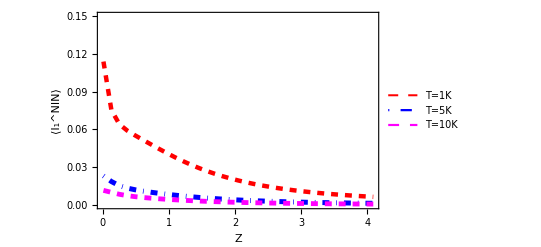

```mathematica
ListLinePlot[{listI0[[All,{1,2}]],listI0[[All,{1,3}]],listI0[[All,{1,4}]]},PlotRange->{0,0.15},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Red,Dashed,Thickness[0.008]},{Blue,DotDashed,Thickness[0.009]},{Magenta,Dashed,Thickness[0.0087]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["T=1K",17,Black,Bold],Style["T=5K",17,Black,Bold],Style["T=10K",17,Black,Bold],Style["T=100K",17,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,18,Bold],FrameLabel-> {Style["Z",22,Black,Bold],Style["⟨I_1^NIN⟩",23,Black,Bold]},LabelStyle->Directive[15]]
```

## Conductance vs Z at Eqbm temp

```mathematica
V1=0.0000;
```

```mathematica
f2e=1/(1+Exp[(Ed-Ef)/kT]); Df0=D[(f2e),{Ed}];kT=k*T;Ef=0.014;k=8.617*10^-5;
```

```mathematica
Df0/.{Z-> 0.1,T-> 1}
```

-(11605. ⅇ^(11605. (-0.014+Ed)))/((1+ⅇ^(11605. (-0.014+Ed)))^2)

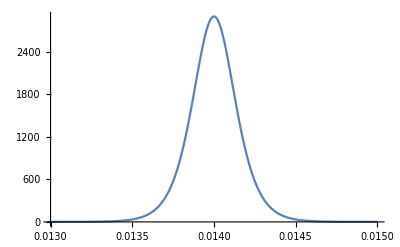

```mathematica
Plot[-Df0/.{Z-> 0.1,T-> 1},{Ed,V1+Ef-.001,V1+Ef+.001}]
```

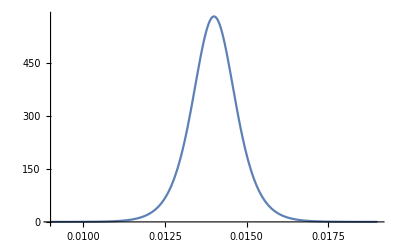

```mathematica
Plot[-Df0/.{T-> 5},{Ed,V1+Ef-.005,V1+Ef+.005}]
```

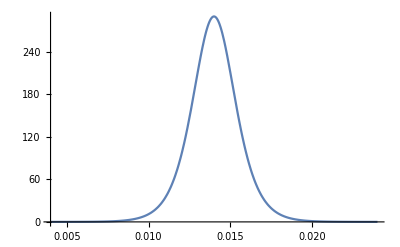

```mathematica
Plot[-Df0/.{T->10},{Ed,V1+Ef-.01,V1+Ef+.01}]
```

```mathematica
Remove["Global`*"];

k=8.617*10^-5;
Ef=0.014;
ke=Piecewise[{{(1+Ed/Ef)^(1/2),Ed>Ef},{(1-Ed/Ef)^(1/2),Ed≤Ef}}]; 
ReeN=Z1^2/(1+Z1^2); 
TeeN=1/(1+Z1^2);
Z1=Z/ke;
FIN=(TeeN);
f2e=1/(1+Exp[(Ed-Ef)/kT]); Df0=D[(f2e),{Ed}];kT=k*T;
V1=0.0;
listNz0=ParallelTable[
thNz0= (NIntegrate[-FIN*Df0/.{T-> 1},{Ed,-Infinity,V1+Ef-0.001}]+NIntegrate[-FIN*Df0/.{T-> 1},{Ed,V1+Ef-0.001,V1+Ef+0.001}]+NIntegrate[-FIN*Df0/.{T-> 1},{Ed,V1+Ef+0.001,Infinity}]); 
thNz10=(NIntegrate[-FIN*Df0/.{T-> 5},{Ed,-Infinity,V1+Ef-0.005}]+NIntegrate[-FIN*Df0/.{T-> 5},{Ed,V1+Ef-0.005,V1+Ef+0.005}]+NIntegrate[-FIN*Df0/.{T-> 5},{Ed,V1+Ef+0.005,Infinity}]); 
thNz20= (NIntegrate[-FIN*Df0/.{T-> 10},{Ed,-Infinity,V1+Ef+-0.01}]+NIntegrate[-FIN*Df0/.{T-> 10},{Ed,V1+Ef-0.01,V1+Ef+0.01}]+NIntegrate[-FIN*Df0/.{T-> 10},{Ed,V1+Ef+0.01,Infinity}]); 
{Z,thNz0,thNz10,thNz20}, {Z,0,4.1,.15}];
listNz0=SortBy[listNz0,First];
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

```mathematica
ListLinePlot[{listNz0[[All,{1,2}]],listNz0[[All,{1,3}]],listNz0[[All,{1,4}]]},PlotRange->All,Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Red,Dashed,Thickness[0.007]},{Blue,Dashed,Thickness[0.008]},{Magenta,Dashed,Thickness[0.0065]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["T=1K",17,Black,Bold],Style["T=5K",17,Black,Bold],Style["T=10K",17,Black,Bold],Style["T=100K",17,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,18,Bold],FrameTicks->{{{{.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{2,"2.0"},{0,"0.0"},{4,"4.0"},{-2,"-2.0"},{-4,"-4.0"}},None}},FrameLabel-> {Style["Z",22,Black,Bold],Style["G^NIN/G^N",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

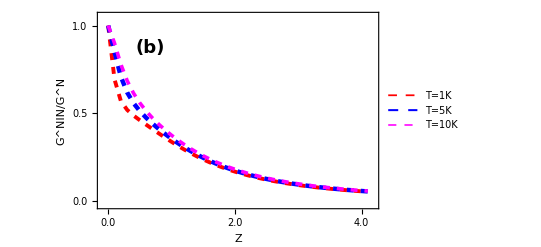

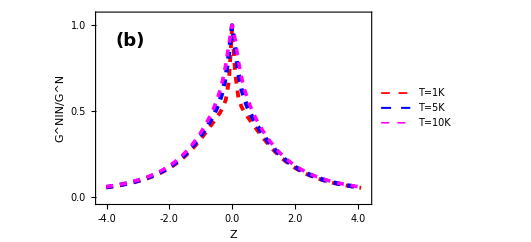

## Shot Noise NIN at (T_1=T_2=0, V_1,V_2=0)

```mathematica
Remove[listFN]
```

```mathematica
DshN=TeeN(1-TeeN);
```

```mathematica
listFNz=ParallelTable[
ShNNz= NIntegrate[DshN,{Ed,0,.0001},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
ShNNz1= NIntegrate[DshN,{Ed,0,0.0005},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
ShNNz2= NIntegrate[DshN,{Ed,0,0.001},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
{Z,ShNNz,ShNNz1,ShNNz2}, {Z,0.01,4.2,.1}];
listFNz=SortBy[listFNz,First]
```

{{0.01,1.003387118×10^-8,5.090433305×10^-8,1.037296259×10^-7},{0.11,1.185378105×10^-6,6.011607698×10^-6,0.00001224439143},{0.21,4.058619113×10^-6,0.00002056472288,0.00004183656457},{0.31,8.022416427×10^-6,0.00004059446417,0.00008243903838},{0.41,0.00001235135178,0.00006239592656,0.0001264382545},{0.51,0.00001641505517,0.00008277249988,0.0001673271035},{0.61,0.00001979695308,0.00009963623913,0.0002009209981},{0.71,0.00002230870298,0.0001120679034,0.0002254437479},{0.81,0.00002393966349,0.0001200472888,0.0002409425764},{0.91,0.0000247871875,0.0001240920892,0.0002485331323},{1.01,0.00002499652769,0.000124951508,0.0002497721109},{1.11,0.00002472038151,0.0001234030547,0.0002462492425},{1.21,0.00002409680685,0.0001201436937,0.0002393741988},{1.31,0.00002324018105,0.0001157468998,0.0002302968172},{1.41,0.00002223987263,0.0001106580517,0.000219903217},{1.51,0.00002116272228,0.0001052083429,0.0002088474777},{1.61,0.00002005693212,0.00009963521042,0.0001975949624},{1.71,0.00001895608124,0.00009410298872,0.0001864650363},{1.81,0.00001788268829,0.0000887210197,0.0001756679927},{1.91,0.00001685113227,0.00008355838116,0.0001653347827},{2.01,0.00001586993563,0.0000786553259,0.0001555399233},{2.11,0.00001494349297,0.00007403189768,0.0001463186362},{2.21,0.00001407335103,0.00006969428018,0.0001376794021},{2.31,0.00001325914038,0.00006563939768,0.0001296130054},{2.41,0.00001249924406,0.00006185820261,0.0001220989621},{2.51,0.00001179127141,0.00005833799461,0.0001151100277},{2.61,0.00001113238956,0.00005506403506,0.0001086153157},{2.71,0.00001051955189,0.000052020654,0.0001025824202},{2.81,9.949652812×10^-6,0.0000491919948,0.00009697883143},{2.91,9.41963006×10^-6,0.00004656250208,0.00009177285216},{3.01,8.926529935×10^-6,0.00004411722939,0.0000869341661},{3.11,8.467546728×10^-6,0.00004184202144,0.00008243416505},{3.21,8.04004421×10^-6,0.00003972360982,0.00007824611136},{3.31,7.641564921×10^-6,0.00003774965032,0.00007434518955},{3.41,7.269831284×10^-6,0.00003590872127,0.00007070848528},{3.51,6.922741377×10^-6,0.00003419029679,0.00006731491796},{3.61,6.598361385×10^-6,0.0000325847047,0.00006414514576},{3.71,6.294916098×10^-6,0.00003108307555,0.00006118145542},{3.81,6.010778421×10^-6,0.00002967728759,0.00005840764564},{3.91,5.744458537×10^-6,0.00002835991052,0.00005580890972},{4.01,5.494593157×10^-6,0.00002712415015,0.00005337172105},{4.11,5.259935128×10^-6,0.00002596379528,0.00005108372388}}

```mathematica
ListLinePlot[{listFNz[[All,{1,2}]],listFNz[[All,{1,3}]],listFNz[[All,{1,4}]]},PlotRange->{0,0.0003},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["V=0.1meV",16,Black,Bold],Style["V=0.5meV",16,Black,Bold],Style["V=1meV",16,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,18,Bold],FrameTicks->{{{{0.0001,"0.1"},{0,"0.0"},{0.0003,"0.3"},{0.0002,"0.2"}},None},{{{1,"1.0"},{2,"2.0"},{0,"0.0"},{3,"3.0"},{4,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["Z",22,Black,Bold],Style["S_(11  sh)^NIN",21,Black,Bold]},LabelStyle->Directive[15,Black],ImagePadding->{{72,10},{60,30}},LabelStyle->{Bold,Large},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,17,Bold],Scaled[{0.07,1.09}]]}]
```

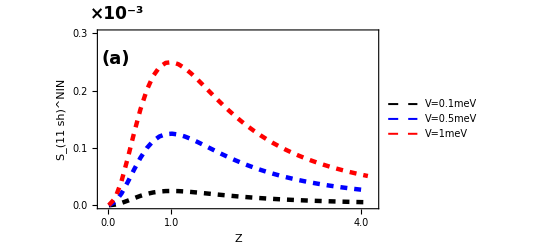

```mathematica
FIN
```

1-Abs[Z/(Z-ⅈ (Piecewise[{{√(1+7.15666 Ed), Ed>0.13973}, {√(1-7.15666 Ed), Ed≤0.13973}, {0, True}}]))]^2

```mathematica
Remove[listFaNz]
```

```mathematica
listFaNz=ParallelTable[
ShNNz= NIntegrate[DshN,{Ed,0,.0001},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
FaN=ShNNz/(NIntegrate[FIN,{Ed,0,.0001},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]);

ShNNz1= NIntegrate[DshN,{Ed,0,0.0005},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
FaN1=ShNNz1/(NIntegrate[FIN,{Ed,0,.0005},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]);

ShNNz2= NIntegrate[DshN,{Ed,0,0.001},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10];
FaN2=ShNNz2/(NIntegrate[FIN,{Ed,0,.001},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]);
 
{Z,FaN,FaN1,FaN2}, {Z,0.01,4.2,.1}];
listFaNz=SortBy[listFaNz,First]
```

{{0.01,0.000100348782,0.000101819033,0.000103740388},{0.11,0.0119977265,0.0121713575,0.0123981053},{0.21,0.0423824648,0.0429764275,0.0437507274},{0.31,0.0879613694,0.089133841,0.0906582705},{0.41,0.144350634,0.146152783,0.148488308},{0.51,0.206999286,0.209389952,0.212477064},{0.61,0.271898254,0.27477597,0.278478284},{0.71,0.335948598,0.339185352,0.343334464},{0.81,0.397028142,0.400495337,0.404924532},{0.91,0.453870765,0.457454759,0.462018544},{1.01,0.505869339,0.509478133,0.51406013},{1.11,0.552875905,0.556439956,0.560953288},{1.21,0.595034552,0.59850445,0.602888257},{1.31,0.632656666,0.635999561,0.640214114},{1.41,0.666135039,0.669330947,0.673352731},{1.51,0.695888587,0.698927088,0.702744518},{1.61,0.722329105,0.725206637,0.728816575},{1.71,0.745842909,0.748560658,0.751965738},{1.81,0.766782059,0.769344364,0.772551003},{1.91,0.785461437,0.787874635,0.790891583},{2.01,0.80215924,0.80443083,0.807268147},{2.11,0.817119288,0.819257346,0.821925694},{2.21,0.830554192,0.832566974,0.835077132},{2.31,0.84264879,0.844544462,0.846907013},{2.41,0.85356353,0.855349997,0.857575123},{2.51,0.863437628,0.865122428,0.867219796},{2.61,0.872391919,0.873982165,0.87596086},{2.71,0.880531381,0.882033732,0.883902235},{2.81,0.887947337,0.889367994,0.891134182},{2.91,0.894719364,0.896064081,0.897735242},{3.01,0.900916937,0.902191033,0.903773897},{3.11,0.90660083,0.907809217,0.909309985},{3.21,0.911824321,0.912971528,0.914395909},{3.31,0.916634223,0.917724421,0.919077667},{3.41,0.921071755,0.922108787,0.923395729},{3.51,0.925173297,0.926160701,0.927385782},{3.61,0.928971027,0.929912061,0.931079371},{3.71,0.932493474,0.93339114,0.934504443},{3.81,0.935765981,0.936623049,0.937685812},{3.91,0.938811119,0.939630141,0.940645559},{4.01,0.941649023,0.942432357,0.943403379},{4.11,0.944297702,0.945047524,0.945976874}}

```mathematica
ListLinePlot[{listFaNz[[All,{1,2}]],listFaNz[[All,{1,3}]],listFaNz[[All,{1,4}]]},PlotRange->{-0.02,1.05},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},FrameTicks->{{{{1.0,"1.0"},{0,"0.0"},{0.5,"0.5"}},None},{{{1,"1.0"},{2,"2.0"},{0,"0.0"},{3,"3.0"},{4,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},PlotLegends->Placed[{Style["V=0.1meV",16,Black,Bold],Style["V=0.5meV",16,Black,Bold],Style["V=1meV",16,Black,Bold]},{Right,Bottom}],FrameTicksStyle->Directive[Black,18,Bold],FrameLabel-> {Style["Z",22,Black,Bold],Style["F^NIN",22,Black,Bold]},LabelStyle->Directive[16,Black]]
```

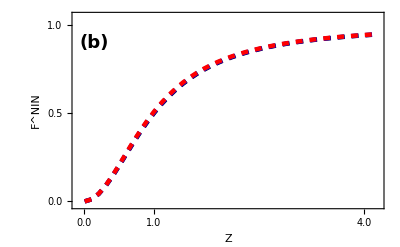

## Thermal Noise NIN at (T_1=T_2=T, V_1=V_2=0)

```mathematica
Remove["Global`*"];

k=8.617*10^-5;
Ef=0.014;
ke=Piecewise[{{(1+Ed/Ef)^(1/2),Ed>Ef},{(1-Ed/Ef)^(1/2),Ed≤Ef}}]; 
ReeN=Z1^2/(1+Z1^2); 
TeeN=1/(1+Z1^2);
Z1=Z/ke;
FIN=(TeeN);
```

```mathematica
f0=1/(1+Exp[(Ed-Ef)/kT]);
```

```mathematica
kT= k*T;
```

```mathematica
DthN=TeeN;
```

```mathematica
Remove[listthN]
```

```mathematica
fth=2f0(1-f0);
```

```mathematica
listthNz=ParallelTable[
thNNz= NIntegrate[2 DthN*fth/.{T-> 1},{Ed,-∞,Ef-0.001}]+NIntegrate[2 DthN*fth/.{T-> 1},{Ed,Ef-0.001,Ef+0.001}]+NIntegrate[2 DthN*fth/.{T-> 1},{Ed,Ef+0.001,∞}]; 
thNNz1= NIntegrate[2 DthN*fth/.{T-> 5},{Ed,-∞,Ef-0.01}]+NIntegrate[2 DthN*fth/.{T-> 5},{Ed,Ef-0.01,Ef+0.01}]+NIntegrate[2 DthN*fth/.{T-> 5},{Ed,Ef+0.01,∞}]; 
thNNz2= NIntegrate[2 DthN*fth/.{T-> 10},{Ed,-∞,Ef-0.01}]+NIntegrate[2 DthN*fth/.{T-> 10},{Ed,Ef-0.01,Ef+0.01}]+NIntegrate[2 DthN*fth/.{T-> 10},{Ed,Ef+0.01,∞}]; 
{Z,thNNz,thNNz1,thNNz2}, {Z,-0.001,4.10,.1}];
listthNz=SortBy[listthNz,First];
```

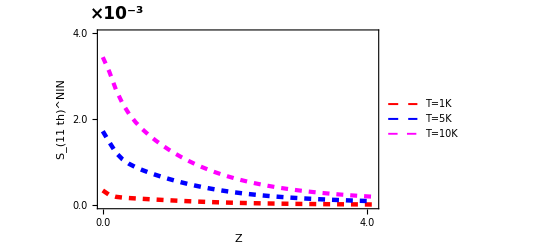

```mathematica
ListLinePlot[{listthNz[[All,{1,2}]],listthNz[[All,{1,3}]],listthNz[[All,{1,4}]]},PlotRange->{0,.004},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Red,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["T=1K",17,Black,Bold],Style["T=5K",17,Black,Bold],Style["T=10K",17,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,18,Bold],FrameTicks->{{{{.004,"4.0"},{0,"0.0"},{.002,"2.0"}},None},{{{-2,"-2.0"},{2,"2.0"},{0,"0.0"},{-4,"-4.0"},{4,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},ImageSize->400,FrameLabel-> {Style["Z",22,Black,Bold],Style["S_(11  th)^NIN",23,Black,Bold]},LabelStyle->Directive[15,Black],ImagePadding->{{72,10},{60,30}},LabelStyle->{Bold,Large},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,17,Bold],Scaled[{0.07,1.09}]]}]
```

```mathematica
listthNz0=ParallelTable[
thNNz= NIntegrate[2 DthN*fth/(4*k*T)/.{T-> 1},{Ed,-∞,Ef-0.001}]+NIntegrate[2 DthN*fth/(4*k*T)/.{T-> 1},{Ed,Ef-0.001,Ef+0.001}]+NIntegrate[2 DthN*fth/(4*k*T)/.{T-> 1},{Ed,Ef+0.001,∞}]; 
thNNz1= NIntegrate[2 DthN*fth/(4*k*T)/.{T-> 5},{Ed,-∞,Ef-0.01}]+NIntegrate[2 DthN*fth/(4*k*T)/.{T-> 5},{Ed,Ef-0.01,Ef+0.01}]+NIntegrate[2 DthN*fth/(4*k*T)/.{T-> 5},{Ed,Ef+0.01,∞}]; 
thNNz2= NIntegrate[2 DthN*fth/(4*k*T)/.{T-> 10},{Ed,-∞,Ef-0.01}]+NIntegrate[2 DthN*fth/(4*k*T)/.{T-> 10},{Ed,Ef-0.01,Ef+0.01}]+NIntegrate[2 DthN*fth/(4*k*T)/.{T-> 10},{Ed,Ef+0.01,∞}];
{Z,thNNz,thNNz1,thNNz2}, {Z,0.01,4.02,.1}];
listthNz0=SortBy[listthNz0,First];
```

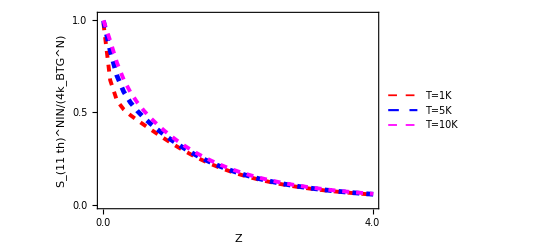

```mathematica
ListLinePlot[{listthNz0[[All,{1,2}]],listthNz0[[All,{1,3}]],listthNz0[[All,{1,4}]]},PlotRange->{0,1.02},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Red,Dashed,Thickness[0.007]},{Blue,Dashed,Thickness[0.0085]},{Magenta,Dashed,Thickness[0.007]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["T=1K",17,Black,Bold],Style["T=5K",17,Black,Bold],Style["T=10K",17,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,18,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{10,"1.0"},{2,"2.0"},{0,"0.0"},{30,"3.0"},{4,"4.0"},{-2,"-2.0"},{-4,"-4.0"}},None}},FrameTicksStyle->Directive[Black,18,Bold],FrameLabel-> {Style["Z",22,Black,Bold],Style["S_(11  th)^NIN/(4k_BTG^N)",23,Black,Bold]},ImageSize->400,LabelStyle->Directive[15,Black]]
```

## Δ_T noise vs. Z in NIN

## Current vs. ΔT at temperature gradient for V =1μV, Z=1,1.5

```mathematica
Remove["Global`*"];

T1=3+T;
T2=3;
V=1*10^-6;
k1=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
Bn=k1^2/(k1^2+Z^2);
kb=8.617*10^-5;
Tc=9.2; 
d=1.764*kb*Tc;  
Ef=10*d;
ds=d;
a1=kb*T2;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[listI1]
listI1={};
ParallelDo[{
f1=1/(1+Exp[(G-Ef-V)/(kb*T1)]);
f2=1/(1+Exp[(G-Ef)/(kb*T2)]);
I1=NIntegrate[Bn(f1-f2)/.{Z-> 1},{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
I2=NIntegrate[Bn(f1-f2)/.{Z-> 1.5},{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
listI=AppendTo[listI1,{T,I1,I2}];
},{T, 0,1.0,.1}];//AbsoluteTiming
listInT=Sort[listI1];
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

{6.66412,Null}

```mathematica
listInT
```

{{0.,4.99998×10^-7,3.07691×10^-7},{0.1,4.86678×10^-7,2.96342×10^-7},{0.2,4.72921×10^-7,2.8462×10^-7},{0.3,4.58728×10^-7,2.72527×10^-7},{0.4,4.44098×10^-7,2.60061×10^-7},{0.5,4.29032×10^-7,2.47223×10^-7},{0.6,4.13528×10^-7,2.34014×10^-7},{0.7,3.97588×10^-7,2.20432×10^-7},{0.8,3.81211×10^-7,2.06478×10^-7},{0.9,3.64398×10^-7,1.92151×10^-7},{1.,3.47147×10^-7,1.77453×10^-7}}

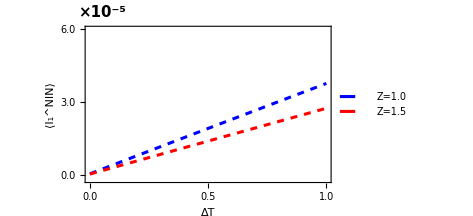

```mathematica
ListLinePlot[{listInT[[All,{1,2}]],listInT[[All,{1,3}]]},Frame->True,PlotRange->{-0.000002,0.00006},PlotLegends->Placed[{Style["Z=1.0",15,Black,Bold],Style["Z=1.5",15,Black,Bold]},{Right,Top}],FrameLabel->{Style["ΔT",18,Bold,Black],Style["⟨I_1^NIN⟩",19,Bold,Black],None,Style["10^3",18,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,15],FrameTicks->{{{{3*10^-5,"3.0"},{6*10^-5,"6.0"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{.5,"0.5"},{04,"4.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.2],Opacity[1],Blue,Dashed],Directive[AbsoluteThickness[2.2],Opacity[1],Red,Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue,DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{72,10},{60,30}},LabelStyle->{Bold,Large},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,15,Bold],Scaled[{0.07,1.09}]]}]
```

## Δ_T noise at temperature gradient

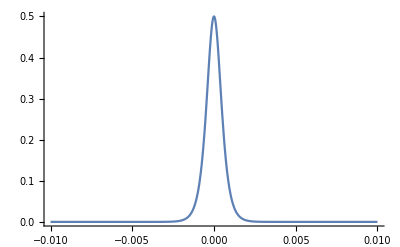

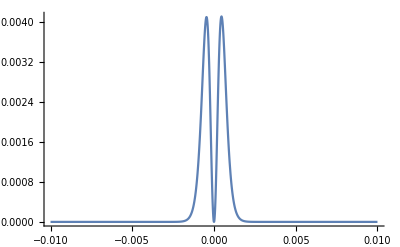

0.00024994

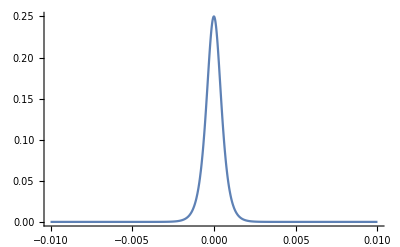

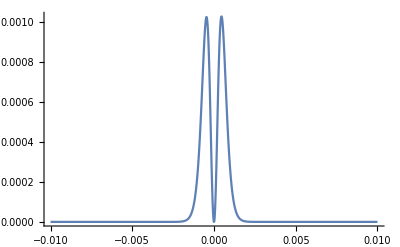

0.00024994

-Graphics-

-Graphics-

```mathematica
f12=1/(1+Exp[(G-V)/(kb*T1)]);
f2=1/(1+Exp[G/(kb*T2)]);
V=0.0000001;T1=4;T2=3;kb=8.617*10^-5;Tc=9.2; d=1.764*kb*Tc; Ef=10*d;
Plot[(f12(1-f12) +f2(1-f2)),{G,V-0.01,V+0.01},PlotRange->All]
Plot[(f12-f2)^2,{G,V-0.01,V+0.01},PlotRange->All]

k1=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
Bn=k1^2/(k1^2+Z^2);
Bn(1-Bn)(f12-f2)^2/.{G-> 0.001,Z-> 1}
Plot[Bn(f12(1-f12) +f2(1-f2))/.{Z-> 1},{G,V-0.01,V+0.01},PlotRange->All]
Plot[Bn(1-Bn)(f12-f2)^2/.{Z-> 1},{G,V-0.01,V+0.01},PlotRange->All]
```

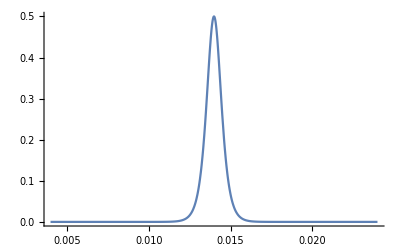

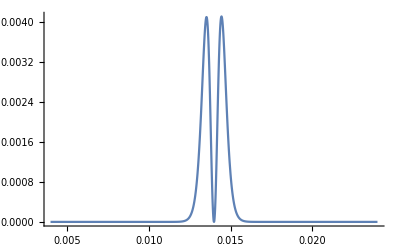

0.

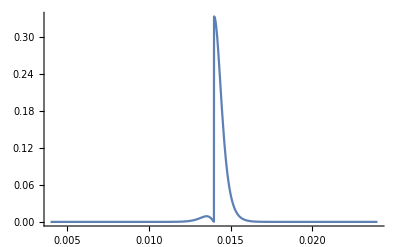

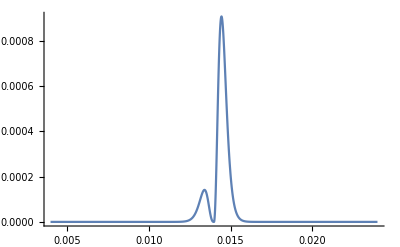

```mathematica
f12=1/(1+Exp[(G-Ef-V)/(kb*T1)]);
f2=1/(1+Exp[(G-Ef)/(kb*T2)]);
V=0.0000001;T1=4;T2=3;kb=8.617*10^-5;Tc=9.2; d=1.764*kb*Tc; Ef=10*d;
Plot[(f12(1-f12) +f2(1-f2)),{G,V+Ef-0.01,V+Ef+0.01},PlotRange->All]
Plot[(f12-f2)^2,{G,V+Ef-0.01,V+Ef+0.01},PlotRange->All]

k1=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
Bn=k1^2/(k1^2+Z^2);
Bn(1-Bn)(f12-f2)^2/.{G-> 0.001,Z-> 1}
Plot[Bn(f12(1-f12) +f2(1-f2))/.{Z-> 1},{G,V+Ef-0.01,V+Ef+0.01},PlotRange->All]
Plot[Bn(1-Bn)(f12-f2)^2/.{Z-> 1},{G,V+Ef-0.01,V+Ef+0.01},PlotRange->All]
```

```mathematica
Remove["Global`*"];

T1=3.5; (*and 3.5 and 4, for ΔT= 0.5 and 1.0*)
T2=3;
k1=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
Bn=k1^2/(k1^2+Z^2);
kb=8.617*10^-5;
Tc=9.2; 
d=1.764*kb*Tc;  
Ef=10*d;
ds=d;
a1=kb*T2;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{
L2=NIntegrate[(Bn)*(G)*df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->100]/(T2);
G2=NIntegrate[(Bn)*df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->100];
Vth2=(-L2*(T1-T2))/G2;
f12=1/(1+Exp[(G-Ef-Vth2)/(kb*T1)]);
f2=1/(1+Exp[(G-Ef)/(kb*T2)]);
Q11NNth=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-Infinity,Vth2+Ef-0.005},Method->"GlobalAdaptive",MaxRecursion->10]+NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,Vth2+Ef-0.005,Vth2+Ef+0.005},Method->"GlobalAdaptive",MaxRecursion->10]+NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,Vth2+Ef+0.005,Infinity},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NNsh=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-Infinity,Vth2+Ef-0.005},Method->"GlobalAdaptive",MaxRecursion->10]+NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,Vth2+Ef-0.005,Vth2+Ef+0.005},Method->"GlobalAdaptive",MaxRecursion->10]+NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,Vth2+Ef+0.005,Infinity},Method->"GlobalAdaptive",MaxRecursion->10];

Q11NN=Q11NNth+Q11NNsh;
list=AppendTo[list1,{Z,Re[Vth2],2*Re[Q11NN],2*Q11NNth,2*Q11NNsh}];
},{Z,0.0,3.0,0.1}];//AbsoluteTiming
listn=Sort[list1];
Export["Dn105e.dat",listn]
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{9.9799,Null}

Dn105e.dat

```mathematica
Import["Dn101e.dat"]
```

{{0.,-1.09408×10^-21,0.00120638,0.00120638,0.},{0.1,5.2129×10^-8,0.000988574,0.000987673,9.01845×10^-7},{0.2,2.02453×10^-7,0.000814419,0.000813084,1.33535×10^-6},{0.3,4.34471×10^-7,0.000713846,0.00071258,1.26549×10^-6},{0.4,7.25476×10^-7,0.000648799,0.000647637,1.16187×10^-6},{0.5,1.05147×10^-6,0.000599949,0.000598823,1.12631×10^-6},{0.6,1.39105×10^-6,0.000558814,0.000557664,1.14987×10^-6},{0.7,1.72749×10^-6,0.000521742,0.000520535,1.20746×10^-6},{0.8,2.04921×10^-6,0.000487212,0.000485934,1.2781×10^-6},{0.9,2.34922×10^-6,0.000454642,0.000453295,1.34749×10^-6},{1.,2.62407×10^-6,0.000423854,0.000422447,1.40701×10^-6},{1.1,2.87279×10^-6,0.000394823,0.000393371,1.45227×10^-6},{1.2,3.09603×10^-6,0.000367568,0.000366086,1.48177×10^-6},{1.3,3.29535×10^-6,0.000342097,0.000340601,1.49585×10^-6},{1.4,3.47278×10^-6,0.000318396,0.0003169,1.49593×10^-6},{1.5,3.6305×10^-6,0.00029642,0.000294936,1.48395×10^-6},{1.6,3.77068×10^-6,0.000276105,0.000274643,1.46204×10^-6},{1.7,3.89535×10^-6,0.000257365,0.000255933,1.43224×10^-6},{1.8,4.00637×10^-6,0.000240106,0.00023871,1.39643×10^-6},{1.9,4.1054×10^-6,0.000224228,0.000222872,1.35624×10^-6},{2.,4.19391×10^-6,0.000209629,0.000208316,1.31307×10^-6},{2.1,4.27321×10^-6,0.000196207,0.000194939,1.26805×10^-6},{2.2,4.34442×10^-6,0.000183868,0.000182646,1.22209×10^-6},{2.3,4.40851×10^-6,0.000172518,0.000171342,1.17594×10^-6},{2.4,4.46634×10^-6,0.000162073,0.000160942,1.13014×10^-6},{2.5,4.51865×10^-6,0.000152452,0.000151367,1.08512×10^-6},{2.6,4.56608×10^-6,0.000143583,0.000142542,1.04121×10^-6},{2.7,4.60918×10^-6,0.000135398,0.0001344,9.98613×10^-7},{2.8,4.64845×10^-6,0.000127838,0.00012688,9.57493×10^-7},{2.9,4.68431×10^-6,0.000120845,0.000119927,9.17943×10^-7},{3.,4.71711×10^-6,0.00011437,0.00011349,8.80016×10^-7}}

## Plots of V_th and Δ_T vs. Z in NIN junction

```mathematica
VthnZ05=Import["Dn105e.dat"][[All,{1,2}]];
VthnZ10=Import["Dn101e.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
A0=ListLinePlot[{VthnZ05,VthnZ10},Frame->True,PlotRange->{-0.0000001,0.000006},Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",14,Black,Bold],Style["ΔT=1.0K",14,Black,Bold]},{Left,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["V_th^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,16],FrameTicks->{{{{0.000003,"3.0"},{0.000006,"6.0"},{0.00002,"0.2"},{-0.0000002,"-0.2"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.2],Opacity[1],Blue],Directive[AbsoluteThickness[2.2],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->340,LabelStyle->Directive[Bold,Black,16,FontFamily->"Times Roman"],ImagePadding->{{70,8},{50,35}}]
```

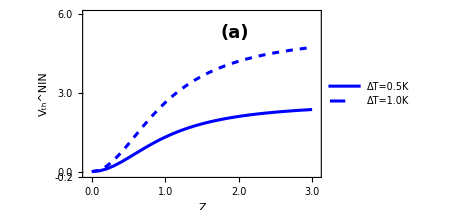

```mathematica
DTnZ05=Import["Dn105e.dat"][[All,{1,3}]];
DTnZ10=Import["Dn101e.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
A2n=ListLinePlot[{DTnZ05,DTnZ10},Frame->True,PlotRange->{{0,3.09},{-0.0000002,0.00125}},Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_T^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,16,FontFamily->"Times Roman"],FrameTicks->{{{{0.0004,"0.4"},{0.0008,"0.8"},{0.0012,"1.2"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.3],Opacity[1],Blue],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15,FontFamily->"Times Roman"],ImageSize->370,LabelStyle->Directive[Bold,Black,15],ImagePadding->{{79,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,17,Bold,FontFamily->"Times Roman"],Scaled[{0.07,1.09}]]}]
```

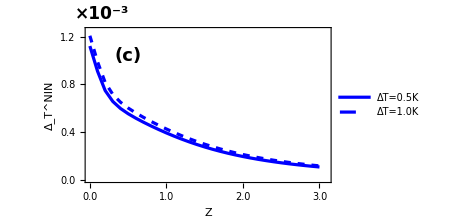

```mathematica
DTthnZ05=Import["Dn105e.dat"][[All,{1,4}]];
DTthnZ10=Import["Dn101e.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
A50=ListLinePlot[{DTthnZ05,DTthnZ10},Frame->True,PlotRange->{{0,3.09},{0,0.0014}},Frame->True,PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_Tth^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,16],FrameTicks->{{{{0.0007,"0.7"},{0.0014,"1.4"},{0,"0.0"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},PlotStyle->{Directive[AbsoluteThickness[2.2],Opacity[1],Blue],Directive[AbsoluteThickness[2.2],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->370,LabelStyle->Directive[Bold,Black,15,FontFamily->"Times Roman"],ImagePadding->{{79,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold,FontFamily->"Times Roman"],Scaled[{0.07,1.09}]]}]
```

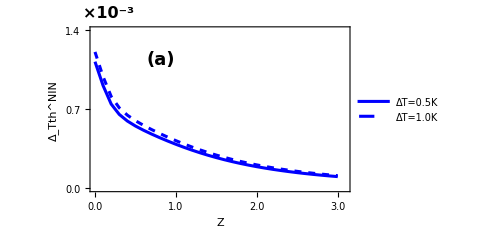

```mathematica
DTshnZ05=Import["Dn105e.dat"][[All,{1,5}]];
DTshnZ10=Import["Dn101e.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
A50=ListLinePlot[{DTshnZ05,DTshnZ10},Frame->True,PlotRange->{{0,3.09},{-0.0000001,0.000004}},PlotLegends->Placed[{Style["ΔT=0.5K",16,Black,Bold],Style["ΔT=1.0K",16,Black,Bold]},{Right,Top}],FrameLabel->{Style["Z",19,Bold,Black],Style["Δ_Tsh^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,16],FrameTicks->{{{{0.00,"0.0"},{2*10^-6,"0.2"},{4*10^-6,"0.4"}},None},{{{1,"1.0"},{0,"0.0"},{2, "2.0"},{3,"3.0"}},None}},
PlotStyle->{Directive[AbsoluteThickness[2.2],Opacity[1],Blue],Directive[AbsoluteThickness[2.2],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[2.3],Opacity[1],Blue, DotDashed]},ImageSize->350,LabelStyle->Directive[Bold,Black,15,FontFamily->"Times Roman"],ImageSize->370,LabelStyle->Directive[Bold,Black,15,FontFamily->"Times Roman"],ImagePadding->{{79,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,16,Bold,FontFamily->"Times Roman"],Scaled[{0.07,1.09}]]}]
```

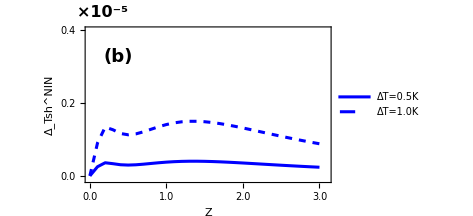

## Δ_T noise vs. ΔT in NIN

```mathematica
Remove["Global`*"];

T1=T;
T2=3;
Z=0;

k1=Piecewise[{{Sqrt[1+G/Ef],G>=Ef},{Sqrt[1-G/Ef],G<Ef}}];
Bn=k1^2/(k1^2+Z^2);
kb=8.617*10^-5;
Tc=9.2; 
d=1.764*kb*Tc;  
Ef=10*d;
ds=d;
a1=kb*T2;
df=Exp[(G)/(a1)]/((Exp[(G)/(a1)]+1)^2 a1);
SetSharedVariable[list1]
list1={};
ParallelDo[{
L2=NIntegrate[(Bn)*(G)*df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->100]/T2;
G2=NIntegrate[(Bn)*df,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->100];
Vth2=(-L2*(T1-T2))/G2;
f11=1/(1+Exp[(G-Ef-Vth1)/(kb*T1)]);
f12=1/(1+Exp[(G-Ef-Vth2)/(kb*T1)]);
f2=1/(1+Exp[(G-Ef)/(kb*T2)]);
(*Q11NNth=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NNsh=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-1000*kb,1000*kb},Method->"GlobalAdaptive",MaxRecursion->10];*)

Q11NNth=NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,-Infinity,Vth2+Ef-0.005},Method->"GlobalAdaptive",MaxRecursion->10]+NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,Vth2+Ef-0.005,Vth2+Ef+0.005},Method->"GlobalAdaptive",MaxRecursion->10]+NIntegrate[Bn(f12(1-f12) +f2(1-f2)),{G,Vth2+Ef+0.005,Infinity},Method->"GlobalAdaptive",MaxRecursion->10];
Q11NNsh=NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,-Infinity,Vth2+Ef-0.005},Method->"GlobalAdaptive",MaxRecursion->10]+NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,Vth2+Ef-0.005,Vth2+Ef+0.005},Method->"GlobalAdaptive",MaxRecursion->10]+NIntegrate[Bn(1-Bn)(f12-f2)^2,{G,Vth2+Ef+0.005,Infinity},Method->"GlobalAdaptive",MaxRecursion->10];

Q11NN=Q11NNth+Q11NNsh;
list=AppendTo[list1,{T,Re[Vth2],2*Re[Q11NN],2*Q11NNth,2*Q11NNsh}];
},{T,3,5,0.12}];//AbsoluteTiming
listn=Sort[list1];
Export["Dn200e.dat",listn]
```

```mathematica
Import["Dn200e.dat"]
```

{{3.,0.,0.00103404,0.00103404,0.},{3.12,-1.3129×10^-22,0.00105472,0.00105472,0.},{3.24,-2.6258×10^-22,0.0010754,0.0010754,0.},{3.36,-3.9387×10^-22,0.00109608,0.00109608,0.},{3.48,-5.2516×10^-22,0.00111676,0.00111676,0.},{3.6,-6.56451×10^-22,0.00113744,0.00113744,0.},{3.72,-7.87741×10^-22,0.00115812,0.00115812,0.},{3.84,-9.19031×10^-22,0.00117881,0.00117881,0.},{3.96,-1.05032×10^-21,0.00119949,0.00119949,0.},{4.08,-1.18161×10^-21,0.00122017,0.00122017,0.},{4.2,-1.3129×10^-21,0.00124085,0.00124085,0.},{4.32,-1.44419×10^-21,0.00126153,0.00126153,0.},{4.44,-1.57548×10^-21,0.00128221,0.00128221,0.},{4.56,-1.70677×10^-21,0.00130289,0.00130289,0.},{4.68,-1.83806×10^-21,0.00132357,0.00132357,0.},{4.8,-1.96935×10^-21,0.00134425,0.00134425,0.},{4.92,-2.10064×10^-21,0.00136493,0.00136493,0.}}

## Plots of V_th and Δ_T vs. ΔT in NIN junction

```mathematica
VthnT0=Import["Dn200e.dat"][[All,{1,2}]];
VthnT1=Import["Dn201e.dat"][[All,{1,2}]];
VthnT3=Import["Dn202e.dat"][[All,{1,2}]];
Needs["PlotLegends`"]
ListLinePlot[{VthnT0,VthnT1,VthnT3},Frame->True,PlotRange->{{3,4.04},{-0.00000005,0.000006}},Frame->True,PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Left,Top}],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["V_th^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,16],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000003,"3.0"},{0.000006,"6.0"},{0.000000,"0.0"},{-0.0000002,"-0.2"},{0,"0.0"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->350,LabelStyle->Directive[Bold,Black,15,FontFamily->"Times Roman"],ImagePadding->{{70,8},{50,40}}]
```

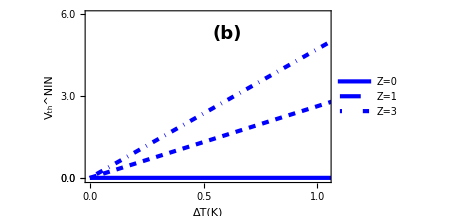

```mathematica
DTnT0=Import["Dn200e.dat"][[All,{1,3}]];
DTnT1=Import["Dn201e.dat"][[All,{1,3}]];
DTnT3=Import["Dn202e.dat"][[All,{1,3}]];
Needs["PlotLegends`"]
ListLinePlot[{DTnT0,DTnT1,DTnT3},Frame->True,PlotRange->{{3,4.05},{0.000,0.0014}},Frame->True,PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Left,Top}],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Δ_T^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,16],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0007,"0.7"},{0.0014,"1.4"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->370,LabelStyle->Directive[Bold,Black,15,FontFamily->"Times Roman"],ImagePadding->{{79,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold,FontFamily->"Times Roman"],Scaled[{0.07,1.09}]]}]
```

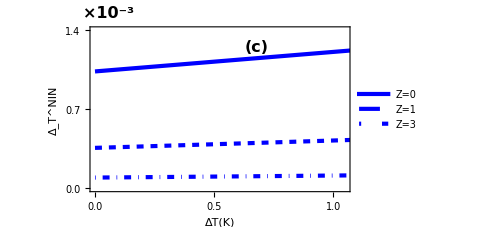

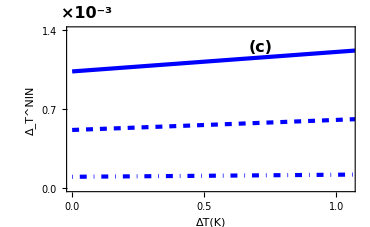

```mathematica
DTthnT0=Import["Dn200e.dat"][[All,{1,4}]];
DTthnT1=Import["Dn201e.dat"][[All,{1,4}]];
DTthnT3=Import["Dn202e.dat"][[All,{1,4}]];
Needs["PlotLegends`"]
ListLinePlot[{DTthnT0,DTthnT1,DTthnT3},Frame->True,PlotRange->{{3,4.05},{0.000,0.0014}},Frame->True,PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Left,Top}],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Δ_Tth^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,16],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.0007,"0.7"},{0.0014,"1.4"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->370,LabelStyle->Directive[Bold,Black,15,FontFamily->"Times Roman"],ImagePadding->{{79,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,16,Bold,FontFamily->"Times Roman"],Scaled[{0.07,1.09}]]}]
```

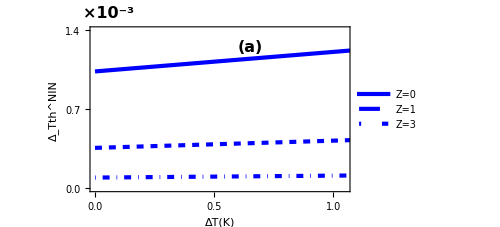

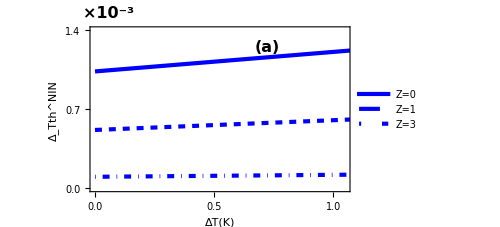

```mathematica
DTshnT0=Import["Dn200e.dat"][[All,{1,5}]];
DTshnT1=Import["Dn201e.dat"][[All,{1,5}]];
DTshnT3=Import["Dn202e.dat"][[All,{1,5}]];
Needs["PlotLegends`"]
ADsn=ListLinePlot[{DTshnT0,DTshnT1,DTshnT3},Frame->True,PlotRange->{{3,4.05},{-0.0000001,0.000003}},Frame->True,PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Left,Top}],FrameLabel->{Style["ΔT(K)",19,Bold,Black],Style["Δ_Tsh^NIN",19,Bold,Black]},FrameTicksStyle->Directive["Label",Black,Bold,16],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},FrameTicks->{{{{0.000,"0.0"},{0.000001,"0.1"},{0.000002,"0.2"},{0.000003,"0.3"}},None},{{{1,"1.0"},{4,"1.0"},{3.5, "0.5"},{3,"0.0"}},None}},ImageSize->370,LabelStyle->Directive[Bold,Black,15,FontFamily->"Times Roman"],ImagePadding->{{79,4},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,16,Bold,FontFamily->"Times Roman"],Scaled[{0.07,1.09}]]}]
```

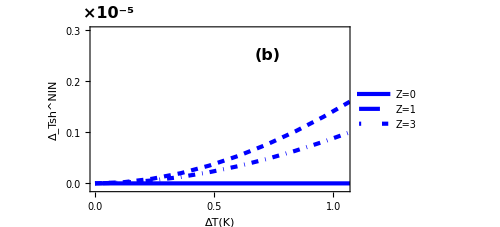

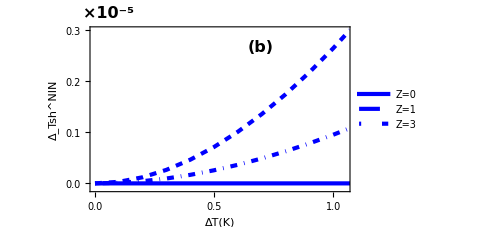

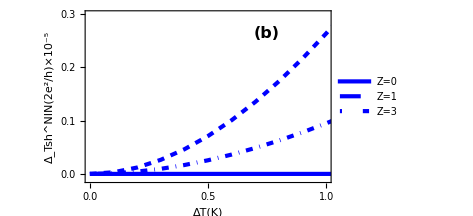

## Quantum shot and thermal noise in NIN and NIS with Andreev approximation

## For incident electron (with Andreev approximation)

```mathematica
Remove["Global`*"];

$Assumptions=Z>0 && T1>0 && T2>0 && Ef> 0 && Δ > 0;
$Assumptions=Ed∈Reals&&Z∈Reals&&T1∈Reals&&T2∈Reals;

k=8.617*10^-5;
Tc=9.2; 
Δ=1.764*k*Tc;

a={{0,-1,u,v},{-1,0,v,u},{0,(-2*Z+I*ke),I*qe*u,-I*qh*v},{(-2 *Z-I*kh),0,I*qe*v,-I*qh*u}};
b={1,0,I*ke+2*Z,0};
{ra,rb,tc,td}=Refine[LinearSolve[a,b],Element[Ed,Reals]]//Simplify;

u1=Piecewise[{{(1/2*(1+I((-Ed^2+Δ^2)/Ed^2)^(1/2)))^(1/2),Ed^2< Δ^2},{(1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed^2≥  Δ^2 }}];

v1=Piecewise[{{(1/2*(1-I((-Ed^2+Δ^2)/Ed^2)^(1/2)))^(1/2),Ed^2< Δ^2},{(1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed^2≥  Δ^2 }}]; 


(*u1=Piecewise[{{(1/2*(Ed+I*(-Ed^2+Δ^2)^(1/2))/Δ)^(1/2),-Δ<Ed<Δ},{(1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed≥ Δ},{(1/2*(1+((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed<-Δ}},1/2^(1/2)];
v1= Piecewise[{{(1/2*(Ed-I*(-Ed^2+Δ^2)^(1/2))/Δ)^(1/2),-Δ<Ed<Δ},{(1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed≥ Δ},{(1/2*(1-((Ed^2-Δ^2)/Ed^2)^(1/2)))^(1/2),Ed<-Δ}},1/2^(1/2)];*)

qe=qh=1;
ke=kh=1;

raS=Simplify[ra/.{u-> u1,v-> v1}];
rbS=Simplify[rb/.{u-> u1,v-> v1}];

raN=Simplify[ra/.{u-> 1,v-> 0}];
rbN=Simplify[rb/.{u->1,v->0}];

{RehS,ReeS}=Abs[{raS,rbS}]^2//Simplify;
{RehN,ReeN}=Abs[{raN,rbN}]^2//Simplify;

FIS=(1+RehS-ReeS)//Simplify;
FIN=(1-ReeN)//Simplify;

DshS=RehS(1-RehS)+ReeS(1-ReeS)+2ReeS*RehS//Simplify;
DshN=ReeN(1-ReeN)//Simplify; 

DthS=(1+RehS-ReeS)//Simplify;
DthN=(1-ReeN)//Simplify;  

Ef=100*Δ;
```

```mathematica
tcS=Simplify[tc/.{u-> u1,v-> v1}];
tdS=Simplify[td/.{u-> u1,v-> v1}];
```

```mathematica
Tees=(Abs[u1]^2-Abs[v1]^2)Abs[tcS]^2//Simplify;
Tehs=(Abs[u1]^2-Abs[v1]^2)Abs[tdS]^2//Simplify;
```

Expression of probabilities

```mathematica
expA=ComplexExpand[Abs[ra]^2]//Simplify
expB=ComplexExpand[Abs[rb]^2]//Simplify
```

(u^2 v^2)/((v^2 Z^2-u^2 (1+Z^2))^2)

((u^2-v^2)^2 Z^2 (1+Z^2))/((v^2 Z^2-u^2 (1+Z^2))^2)

```mathematica
expC=(Abs[u]^2-Abs[v]^2)ComplexExpand[Abs[tc]^2]//Simplify
expD=(Abs[u]^2-Abs[v]^2)ComplexExpand[Abs[td]^2]//Simplify
```

(u^2 (1+Z^2) (Abs[u]^2-Abs[v]^2))/((v^2 Z^2-u^2 (1+Z^2))^2)

(v^2 Z^2 (Abs[u]^2-Abs[v]^2))/((v^2 Z^2-u^2 (1+Z^2))^2)

```mathematica
P=RehS+ReeS+Tees+Tehs;
```

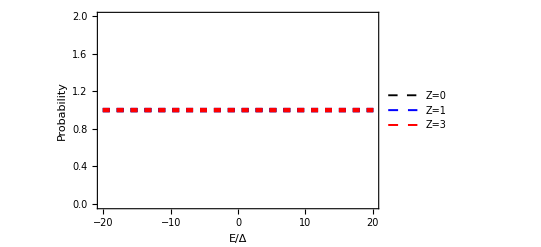

```mathematica
Plot[{P/.{Z-> 0},P/.{Z-> 1},P/.{Z-> 30}},{Ed,-20.09,20.09},PlotRange->{-0.01,2},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,19,Bold],FrameLabel-> {Style["E/Δ",22,Black,Bold],Style["Probability",23,Black,Bold,Italic]},LabelStyle->Directive[Bold,20,Large]]
```

## Prob and G NIS

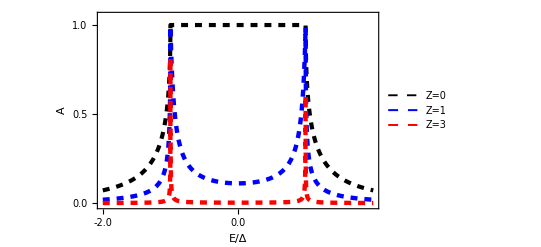

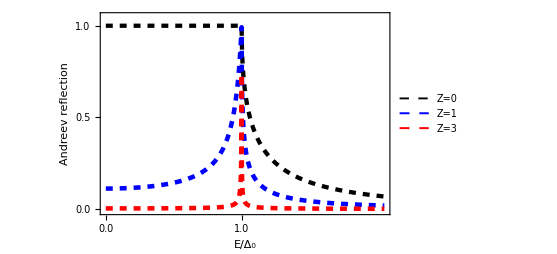

```mathematica
Plot[{RehS/.{Z-> 0},RehS/.{Z-> 1},RehS/.{Z-> 3}},{Ed,-2*Δ,2*Δ},PlotRange->{-0.01,1.05},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,19,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{-2*Δ,"-2.0"},{2*Δ,"2.0"},{0,"0.0"},{Δ,"1.0"},{15,"15.0"},{-Δ,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["E/Δ",22,Black,Bold],Style["A",23,Black,Bold,Italic]},LabelStyle->Directive[Bold,20,Large]]
```

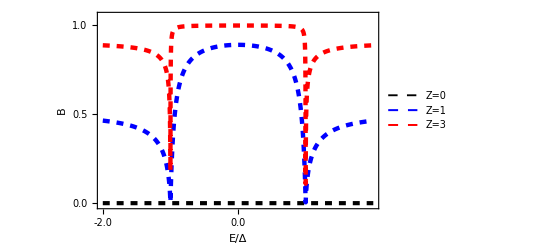

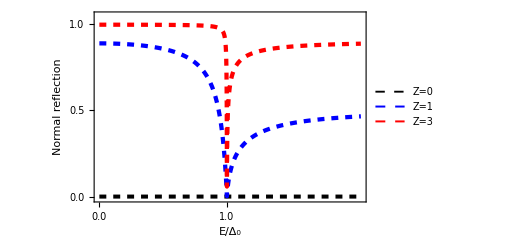

```mathematica
Plot[{ReeS/.{Z-> 0},ReeS/.{Z-> 1},ReeS/.{Z-> 3}},{Ed,-2*Δ,2*Δ},PlotRange->{-0.01,1.05},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,19,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{-2*Δ,"-2.0"},{2*Δ,"2.0"},{0,"0.0"},{Δ,"1.0"},{15,"15.0"},{-Δ,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["E/Δ",22,Black,Bold],Style["B",23,Black,Bold,Italic]},LabelStyle->Directive[Bold,20,Large]]
```

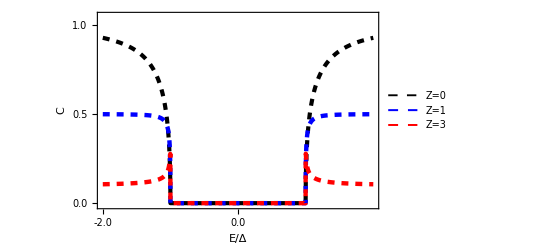

```mathematica
Plot[{Tees/.{Z-> 0},Tees/.{Z-> 1},Tees/.{Z-> 3}},{Ed,-2*Δ,2*Δ},PlotRange->{-0.01,1.05},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,19,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{-2*Δ,"-2.0"},{2*Δ,"2.0"},{0,"0.0"},{Δ,"1.0"},{15,"15.0"},{-Δ,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["E/Δ",22,Black,Bold],Style["C",23,Black,Bold,Italic]},LabelStyle->Directive[Bold,20,Large]]
```

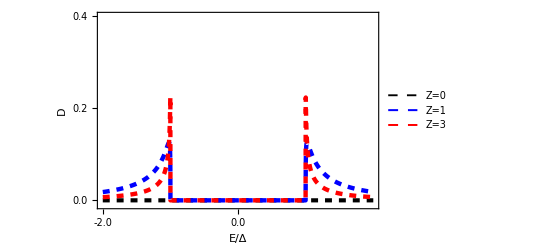

```mathematica
Plot[{Tehs/.{Z-> 0},Tehs/.{Z-> 1},Tehs/.{Z-> 3}},{Ed,-2*Δ,2*Δ},PlotRange->{-0.01,.4},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,19,Bold],FrameTicks->{{{{0.4,"0.4"},{0,"0.0"},{0.2,"0.2"}},None},{{{-2*Δ,"-2.0"},{2*Δ,"2.0"},{0,"0.0"},{Δ,"1.0"},{15,"15.0"},{-Δ,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["E/Δ",22,Black,Bold],Style["D",23,Black,Bold,Italic]},LabelStyle->Directive[Bold,20,Large]]
```

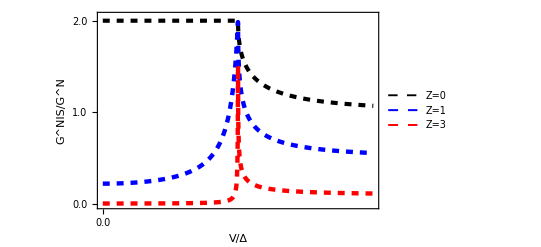

```mathematica
Plot[{FIS/.{Z-> 0},FIS/.{Z-> 1},FIS/.{Z-> 3}},{Ed,.0,2*Δ},PlotRange->{-0.01,2.05},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["Z=0",16,Black,Bold],Style["Z=1",16,Black,Bold],Style["Z=3",16,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,19,Bold],FrameTicks->{{{{2.0,"2.0"},{0,"0.0"},{1,"1.0"}},None},{{{-2*Δ,"-2.0"},{2*Δ,"2.0"},{0,"0.0"},{Δ,"1.0"},{15,"15.0"},{-Δ,"-1.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["V/Δ",22,Black,Bold],Style["G^NIS/G^N",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

## Prob and G NIN (u=1,v=0,Δ=0)

```mathematica
\   [ScriptCapitalT]
```

```mathematica
ℛ
```

```mathematica
Plot[{1-ReeN,ReeN},{Z,.0,4.05},PlotRange->{-0.01,1.05},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["𝒯",18,Black,Bold],Style["ℛ",18,Black,Bold],Style["Z=3",18,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,19,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{1,"1.0"},{2,"2.0"},{0,"0.0"},{3,"3.0"},{15,"15.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["Z",22,Black,Bold],Style["",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

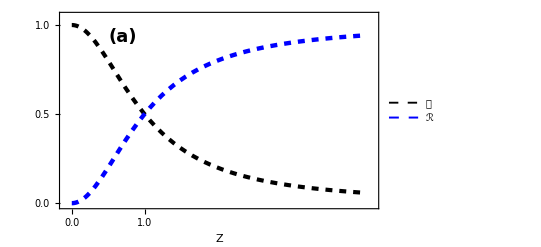

Conductance in NIN jun. for Energy independent transmission probability

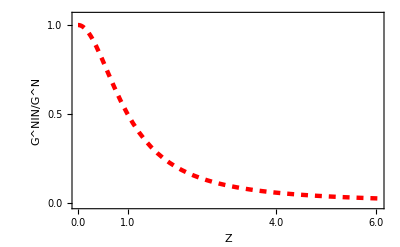

```mathematica
Plot[{FIN},{Z,.0,6.05},PlotRange->{-0.01,1.05},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Red,Dashed,Thickness[0.0079]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,19,Bold],FrameTicks->{{{{0.5,"0.5"},{0,"0.0"},{1,"1.0"}},None},{{{1,"1.0"},{2,"2.0"},{0,"0.0"},{3,"3.0"},{4,"4.0"},{5,"5.0"},{6,"6.0"}},None}},FrameLabel-> {Style["Z",22,Black,Bold],Style["G^NIN/G^N",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

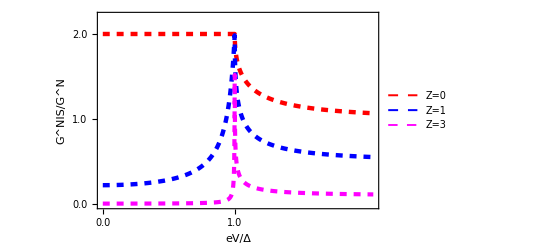

```mathematica
Plot[{(FIS/FIN)/(1+Z^2)/.{Z-> 0},(FIS/FIN)/(1+Z^2)/.{Z-> 1},(FIS/FIN)/(1+Z^2)/.{Z-> 3}},{Ed,.0,2.05},PlotRange->{-0.01,2.21},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Red,Dashed,Thickness[0.0079]},{Blue,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,19,Bold],PlotLegends->Placed[{Style["Z=0",18,Black,Bold],Style["Z=1",18,Black,Bold],Style["Z=3",18,Black,Bold]},{Right,Top}],FrameTicks->{{{{1,"1.0"},{3,"3.0"},{2.0,"2.0"},{0,"0.0"},{4,"4.0"}},None},{{{1,"1.0"},{2,"2.0"},{0,"0.0"},{3,"3.0"},{4,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["eV/Δ",22,Black,Bold],Style["G^NIS/G^N",20,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

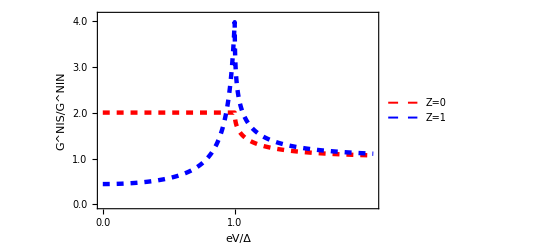

```mathematica
Plot[{(FIS/FIN)/.{Z-> 0},(FIS/FIN)/.{Z-> 1}},{Ed,.0,2.05},PlotRange->{-0.01,4.1},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Red,Dashed,Thickness[0.0079]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},FrameTicksStyle->Directive[Black,19,Bold],PlotLegends->Placed[{Style["Z=0",18,Black,Bold],Style["Z=1",18,Black,Bold],Style["Z=3",18,Black,Bold]},{Right,Top}],FrameTicks->{{{{1,"1.0"},{3,"3.0"},{2.0,"2.0"},{0,"0.0"},{4,"4.0"}},None},{{{1,"1.0"},{2,"2.0"},{0,"0.0"},{3,"3.0"},{4,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["eV/Δ",22,Black,Bold],Style["G^NIS/G^NIN",23,Black,Bold]},LabelStyle->Directive[Bold,20,Large]]
```

## Shot Noise NIS (T_1=T_2=0, V_1,V_2=0)

```mathematica
Remove[listFS]
```

```mathematica
listFS=ParallelTable[
Z=0.01;
ShNS= NIntegrate[DshS,{Ed,0,V},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
FaNS=ShNS/(NIntegrate[FIS ,{Ed,0,V},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]);
{V,ShNS,FaNS}, {V,0.01*Δ,4.02*Δ,.2*Δ}];
listFS=SortBy[listFS,First]
```

CloudConnect::vwarn: This version of Mathematica will no longer be supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.0000139844,2.23585711×10^-8,0.000799733416},{0.000293671,4.626486855×10^-7,0.000788008113},{0.000573359,8.654013419×10^-7,0.000754962152},{0.000853046,1.194852039×10^-6,0.000700590036},{0.00113273,1.415208123×10^-6,0.000624882716},{0.00141242,1.490635023×10^-6,0.000527827591},{0.00169211,0.00006783779904,0.0210670553},{0.00197179,0.0001153999504,0.0324036063},{0.00225148,0.0001499511705,0.0386322981},{0.00253117,0.0001762029509,0.0420515558},{0.00281086,0.0001961102494,0.0436426186},{0.00309054,0.0002135691776,0.0445972934},{0.00337023,0.0002273844851,0.0447217057},{0.00364992,0.0002389729815,0.0444509332},{0.0039296,0.0002488680641,0.0439349131},{0.00420929,0.0002574105267,0.0432305027},{0.00448898,0.000264472296,0.042368421},{0.00476867,0.0002714407587,0.0415946167},{0.00504835,0.0002772547691,0.0406950549},{0.00532804,0.000282448038,0.0397894842},{0.00560773,0.0002868502668,0.0388510068}}

```mathematica
listFS1=ParallelTable[
Z=0.5;
ShNS1= NIntegrate[DshS,{Ed,0,V},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
FaNS1=ShNS1/(NIntegrate[FIS,{Ed,0,V},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]);
{V,ShNS1,FaNS1}, {V,0.01*Δ,4.02*Δ,.2*Δ}];
listFS1=SortBy[listFS1,First]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.0000139844,0.00001381176173,1.11109465},{0.000293671,0.0002904978924,1.10369416},{0.000573359,0.0005691091016,1.08098984},{0.000853046,0.0008478290164,1.03629357},{0.00113273,0.001109234698,0.951512426},{0.00141242,0.001253745863,0.769458589},{0.00169211,0.00134863062,0.681405974},{0.00197179,0.001428490935,0.630727519},{0.00225148,0.001498561878,0.592689133},{0.00253117,0.001562123173,0.561824865},{0.00281086,0.001621740731,0.535571038},{0.00309054,0.001680154117,0.514461884},{0.00337023,0.001732942008,0.49431321},{0.00364992,0.001785902719,0.477374208},{0.0039296,0.001837650878,0.462328621},{0.00420929,0.001888461461,0.448885346},{0.00448898,0.001937836847,0.436567273},{0.00476867,0.001987873423,0.425822088},{0.00504835,0.002036929803,0.41590577},{0.00532804,0.002085163983,0.406738771},{0.00560773,0.002132699463,0.398231244}}

```mathematica
listFS2=ParallelTable[
Z=1;
ShNS2= NIntegrate[DshS,{Ed,0,V},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
FaNS2=ShNS2/(NIntegrate[FIS,{Ed,0,V},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]);
{V,ShNS2,FaNS2}, {V,0.01*Δ,4.02*Δ,.2*Δ}];
listFS2=SortBy[listFS2,First]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.0000139844,5.52482747×10^-6,1.77777119},{0.000293671,0.0001173722269,1.77477173},{0.000573359,0.0002372167556,1.76504683},{0.000853046,0.0003764148542,1.74314222},{0.00113273,0.0005585986472,1.68631492},{0.00141242,0.0007911966922,1.31314339},{0.00169211,0.0009080577358,1.05602727},{0.00197179,0.001006978145,0.957756219},{0.00225148,0.001096578499,0.895940413},{0.00253117,0.001180966192,0.852178661},{0.00281086,0.001262065838,0.817286837},{0.00309054,0.001340671443,0.789569169},{0.00337023,0.0014178519,0.766824096},{0.00364992,0.001493743962,0.747557325},{0.0039296,0.001568761019,0.731059141},{0.00420929,0.001643054681,0.716744846},{0.00448898,0.001716855249,0.704219137},{0.00476867,0.001790070709,0.693038077},{0.00504835,0.001862930801,0.683175132},{0.00532804,0.001939216231,0.675437993},{0.00560773,0.002007790779,0.665890248}}

```mathematica
listFS4=ParallelTable[
Z=3;
ShNS4= NIntegrate[DshS,{Ed,0,V},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
FaNS4=ShNS4/(NIntegrate[FIS,{Ed,0,V},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]);
{V,ShNS4,FaNS4}, {V,0.01*Δ,4.02*Δ,.2*Δ}];
listFS4=SortBy[listFS4,First]
```

```mathematica
ListLinePlot[{listFS[[All,{1,2}]],listFS1[[All,{1,2}]],listFS2[[All,{1,2}]],listFS4[[All,{1,2}]]},PlotRange->All,Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Magenta,Dashed,Thickness[0.0079]},{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["Z=0.01",15,Black],Style["Z=0.5",15,Black],Style["Z=1",15,Black],Style["Z=3",15,Black]},{Left,Top}],FrameTicksStyle->Directive[Black,19,Bold,FontFamily->"Times Roman"],FrameTicks->{{{{0.002,"2.0"},{0,"0.0"},{0.001,"1.0"}},None},{{{Δ,"1.0"},{2*Δ,"2.0"},{0,"0.0"},{3*Δ,"3.0"},{4*Δ,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["V/Δ",22,Black,Bold],Style["S_(11  sh)^NIS",21,Black,Bold]},LabelStyle->Directive[16,Bold,FontFamily->"Times Roman"],ImagePadding->{{77,8},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-5",Black,17,Bold,FontFamily->"Times Roman"],Scaled[{0.07,1.09}]]}]
```

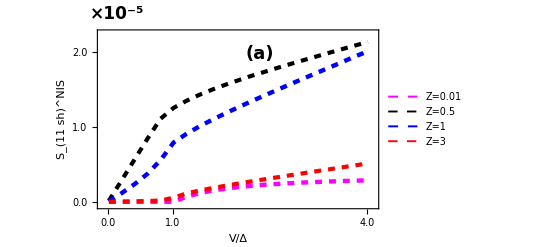

```mathematica
ListLinePlot[{listFS[[All,{1,3}]],listFS1[[All,{1,3}]],listFS2[[All,{1,3}]],listFS4[[All,{1,3}]]},PlotRange->{-0.05,2.1},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Magenta,Dashed,Thickness[0.0079]},{Black,Dashed,Thickness[0.0075]},{Blue,Dashed,Thickness[0.0079]},{Red,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["Z=0.01",15,Black,Bold],Style["Z=0.5",15,Black,Bold],Style["Z=1",15,Black,Bold],Style["Z=3",15,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,19,Bold,FontFamily->"Times Roman"],FrameTicks->{{{{2.0,"2.0"},{0,"0.0"},{1,"1.0"}},None},{{{Δ,"1.0"},{2*Δ,"2.0"},{0,"0.0"},{3*Δ,"3.0"},{4*Δ,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["V/Δ",22,Black,Bold,FontFamily->"Times Roman"],Style["F^NIS",21,Black,Bold,FontFamily->"Times Roman"]},LabelStyle->Directive[15,Black,Bold,FontFamily->"Times Roman"]]
```

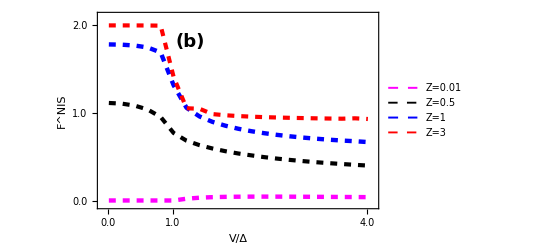

```mathematica
Remove[listFNS]
```

```mathematica
listFNSz=ParallelTable[
ShNSz= NIntegrate[DshS,{Ed,0,.0001},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
ShNSz1= NIntegrate[DshS,{Ed,0,0.0005},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
ShNSz2= NIntegrate[DshS,{Ed,0,0.001},Method->{"GlobalAdaptive","SingularityHandler"->None,"MaxErrorIncreases"->5000,"SymbolicProcessing"->0},MaxRecursion->50,WorkingPrecision->10]; 
{Z,ShNSz,ShNSz1,ShNSz2}, {Z,0.01,4.1,.1}];
listFNSz=SortBy[listFNSz,First]
```

{{0.01,1.596157413×10^-7,7.653995199×10^-7,1.326504487×10^-6},{0.11,0.00001777943117,0.00008556971825,0.0001497223746},{0.21,0.0000524753032,0.0002547642973,0.0004564950839},{0.31,0.00008336713025,0.0004094198059,0.0007589615747},{0.41,0.00009853538044,0.0004897353995,0.000943917312},{0.51,0.00009821134452,0.0004934507034,0.0009889851978},{0.61,0.00008831487023,0.000447751069,0.0009300118733},{0.71,0.00007465501008,0.0003811991543,0.0008163063879},{0.81,0.0000608890056,0.000312601265,0.0006862744448},{0.91,0.00004871815522,0.0002511382821,0.0005622962935},{1.01,0.00003864631008,0.0001998247741,0.0004542899902},{1.11,0.00003059748749,0.0001585658833,0.0003647448041},{1.21,0.00002427840925,0.0001260314698,0.0002925226751},{1.31,0.00001935517656,0.0001006025189,0.0002351139577},{1.41,0.00001552543852,0.00008077463394,0.0001897767935},{1.51,0.00001253987207,0.00006528976857,0.0001540247842},{1.61,0.0000102020879,0.00005314823522,0.0001257818222},{1.71,8.360970979×10^-6,0.00004357621907,0.0001033864084},{1.81,6.901553807×10^-6,0.0000359825108,0.00008553867054},{1.91,5.736745937×10^-6,0.00002991786112,0.00007123344566},{2.01,4.800577138×10^-6,0.0000250411691,0.00005969739393},{2.11,4.042945014×10^-6,0.00002109291188,0.00005033610424},{2.21,3.425635831×10^-6,0.00001787486949,0.00004269193814},{2.31,2.919349313×10^-6,0.00001523488809,0.00003641138222},{2.41,2.501487205×10^-6,0.0000130555123,0.00003122015244},{2.51,2.154511964×10^-6,0.00001124552433,0.00002690435741},{2.61,1.86472701×10^-6,9.733642415×10^-6,0.00002329628978},{2.71,1.621367444×10^-6,8.463815192×10^-6,0.00002026370949},{2.81,1.415919318×10^-6,7.391693912×10^-6,0.00001770174522},{2.91,1.241607472×10^-6,6.48197527×10^-6,0.00001552675485},{3.01,1.093008088×10^-6,5.706389443×10^-6,0.00001367165201},{3.11,9.657539252×10^-7,5.042168251×10^-6,0.00001208233229},{3.21,8.563087553×10^-7,4.470872198×10^-6,0.00001071492668},{3.31,7.617937491×10^-7,3.977487172×10^-6,9.533679962×10^-6},{3.41,6.798530666×10^-7,3.549724816×10^-6,8.509303218×10^-6},{3.51,6.085492056×10^-7,3.177477589×10^-6,7.617687716×10^-6},{3.61,5.462810625×10^-7,2.852391946×10^-6,6.838895724×10^-6},{3.71,4.917194255×10^-7,2.567532238×10^-6,6.156364494×10^-6},{3.81,4.437559202×10^-7,2.317114629×10^-6,5.556275217×10^-6},{3.91,4.01462395×10^-7,2.096295389×10^-6,5.027050297×10^-6},{4.01,3.640584488×10^-7,1.901001585×10^-6,4.558950907×10^-6}}

```mathematica
ListLinePlot[{listFNSz[[All,{1,2}]],listFNSz[[All,{1,3}]],listFNSz[[All,{1,4}]]},PlotRange->{-0.00003,0.00108},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Black,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Red,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["V=0.1meV",17,Black,Bold],Style["V=0.5meV",17,Black,Bold],Style["V=1meV",17,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,18,Bold],FrameTicks->{{{{0.001,"1.0"},{0,"0.0"},{0.0005,"0.5"}},None},{{{1,"1.0"},{2,"2.0"},{0,"0.0"},{3,"3.0"},{4,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["Z",22,Black,Bold],Style["S_(11  sh)^NIS",21,Black,Bold]},LabelStyle->Directive[16,Bold,FontFamily->"Times Roman"],ImagePadding->{{77,8},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,17,Bold,FontFamily->"Times Roman"],Scaled[{0.07,1.09}]]}]
```

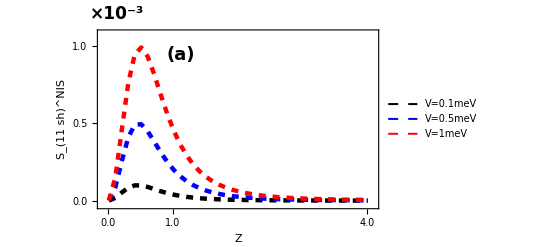

## Thermal Noise NIS (T_1=T_2=T, V_1=V_2=0)

```mathematica
f0=1/(1+Exp[Ed/kT]);
```

```mathematica
kT= k*T;
```

```mathematica
k=8.617*10^-5;
```

```mathematica
Remove[listthNS]
```

```mathematica
fth=2f0(1-f0);
```

To check with conductance

```mathematica
listthNSz0=ParallelTable[
thNSz= NIntegrate[DthS*fth/.{T-> 1},{Ed,-∞,Ef-0.01}]+NIntegrate[DthS*fth/.{T-> 1},{Ed,Ef-0.01,Ef+0.01}]+NIntegrate[DthS*fth/.{T-> 1},{Ed,Ef+0.01,∞}]; 
thNSz1= NIntegrate[DthS*fth/.{T-> 5},{Ed,-∞,Ef-0.01}]+ NIntegrate[DthS*fth/.{T-> 5},{Ed,-Ef-0.01,E+0.01}]+ NIntegrate[DthS*fth/.{T-> 5},{Ed,Ef+0.01,∞}]; 
thNSz2= NIntegrate[DthS*fth/.{T-> 10},{Ed,-∞,Ef-0.1}]+ NIntegrate[DthS*fth/.{T-> 10},{Ed,-Ef-0.01,E+0.1}]+ NIntegrate[DthS*fth/.{T-> 10},{Ed,Ef+0.1,∞}]; 
{Z,thNSz,thNSz1,thNSz2}, {Z,0.01,4.1,0.1}];
listthNSz0=SortBy[listthNSz0,First];
```

```mathematica
ListLinePlot[{listthNSz0[[All,{1,2}]],listthNSz0[[All,{1,3}]],listthNSz0[[All,{1,4}]]},PlotRange->{-0.00006,0.008},Frame->True,FrameStyle->Thickness[0.004],Axes->False,PlotStyle->{{Red,Dashed,Thickness[0.008]},{Blue,Dashed,Thickness[0.008]},{Magenta,Dashed,Thickness[0.0079]},{Magenta,Dashed,Thickness[0.0075]}},PlotLegends->Placed[{Style["T=1K",17,Black,Bold],Style["T=5K",17,Black,Bold],Style["T=10K",17,Black,Bold]},{Right,Top}],FrameTicksStyle->Directive[Black,18,Bold],FrameTicks->{{{{0.008,"8.0"},{0,"0.0"},{0.004,"4.0"}},None},{{{1,"1.0"},{2,"2.0"},{0,"0.0"},{3,"3.0"},{4,"4.0"},{-10,"-10.0"},{-15,"-15.0"}},None}},FrameLabel-> {Style["Z",22,Black,Bold],Style["S_(11  th)^NIS",21,Black,Bold]},LabelStyle->Directive[16,Bold,FontFamily->"Times Roman"],ImagePadding->{{77,8},{70,35}},PlotRangeClipping->False,Epilog->{Text[Style["×10^-3",Black,17,Bold,FontFamily->"Times Roman"],Scaled[{0.07,1.09}]]}]
```